# DIAMOND Light Source Beamlines

Survey of DIAMOND light source beamlines in the energy range 30 - 180 keV for comparison against the possible operating range of the Lyncean CLS-300.

```mathematica
F01conv=1.5*10^-3;
```

## CBETA ICS

```mathematica
CBETA={{32.2,109.7,233.1,402.5},{F01conv*3.16*10^10,F01conv*3.20*10^10,F01conv*3.21*10^10,F01conv*3.22*10^10}};
```

## Lyncean CLS-300

Using Geoff Krafft’s rule of thumb for a Thomson scattering spectra [Krafft + Priebe, Compton Sources of Electromagnetic Radiation, Reviews Of Accelerator Science And Technology: Volume 3: Accelerators as Photon Sources. (2010)]  F_(0.1%)=1.5×10^-3 F. We can work out where the CLS-300 would sit on this plot

```mathematica
CLS300={{90,180},{F01conv*4*10^12,F01conv*4*10^12}};
```

## Example Source

```mathematica
ExampleSource={{89.9,179},{F01conv*1.60*10^12,F01conv*8.04*10^11}};
```

## DIAMOND Beamline Parameters

```mathematica
I12JEEP={{53,90,180},{1.8*10^11,8*10^10,3*10^9}};
```

I12 (JEEP) is the highest energy DIAMOND beamline. 4.2T superconducting wiggler, mono-chromatic 53-150 keV. Data from [M. Drakopoulos et al, Beamline I12 (Jeep) at the Diamond Light Source, Journal of Syncrotron Radiation, 22 (2015)]. This plot has weird units that don’t chime with the paper, I wonder if that is where all the weird units stem from?

```mathematica
I15={{30},{10^12}};
```

No good data available on the I15 Extreme Conditions beam line, which is quoted from (20 - 80 keV). [D.R. Allan Status of the Crystallography Beamlines at the Diamond light source, Eur. Phys. Journal.Plus, 130:56 (2015)]. Maybe email the head scientist?

```mathematica
I15XPDF={{76.7},{10^12}};
```

This beamline data is slightly dubious, on the website the I15 XPDF is rated for 40, 65, 76.7 keV but no more data can be found. Data comes from [P. Charter, XPDF: The new X-ray Pair Distribution Function Beamline at Diamond, EPDIC’15, Bari, Italy (2015)].

```mathematica
I07={{30},{6*10^11}};
```

Good data from the I07 Surface and Interface Diffraction Beamline rated from (6-30 keV). Data from [C. Nicklin, Diamond Beamline I07: A Beamline for Surface and Interface Diffraction. Journal of Synchrotron Radiation, 23 (2016)].

```mathematica
I13={{30},{10^14}};
```

Diamond - Manchester University collaborative beamline (6 - 30 keV). Diamonds longest insertion device. Data from [C. Rau, Coherent Imaging at the Diamond Beamline I13, Phys. Status. Solidi. A, 11 (2011)].

```mathematica
B16={{45},{7*10^11}};
```

General purpose, flexible test beamline. Data found at [K.J.S. Sawhney et al, A Test Beamline on Diamond Light Source, AIP Conference Proceedings, 1234, 387 (2010)].

```mathematica
B18={{35},{5*10^11}};
```

X-ray Absorption Spectroscopy beamline. Data found at [A.J. Dent et al, B18: A Core XAS Spectroscopy Beamline for Diamond, Journal of Physics: Conference Series, 190, 012039 (2009)].

## Flux 0.1% BW Plot

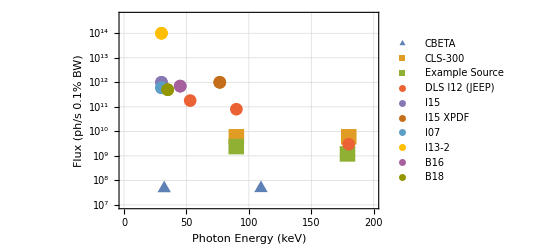

```mathematica
ListLogPlot[{Transpose[CBETA],Transpose[CLS300],Transpose[ExampleSource],Transpose[I12JEEP],Transpose[I15],Transpose[I15XPDF],Transpose[I07],Transpose[I13],Transpose[B16],Transpose[B18]},Frame->True,FrameLabel->{"Photon Energy (keV)","Flux (ph/s 0.1% BW)"},LabelStyle->15,GridLines->Automatic,PlotMarkers->{{▲,16},{■,16},{■,16},{●,13},{●,13},{●,13},{●,13},{●,13},{●,13},{●,13}},PlotRange->{{0,200},{10^7,5*10^14}},PlotLegends->{"CBETA","CLS-300","Example Source","DLS I12 (JEEP)","I15","I15 XPDF","I07","I13-2","B16","B18"}]
```